## Execute everything here

Note that all persistence lengths need to be further normalized with the filament length L

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dat1=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence31.5.mx"];
dat2=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence63..mx"];
dat3=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence126..mx"];
dat4=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence200..mx"];
dat5=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence400..mx"];
dat6=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence800..mx"];
dat7=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence2000..mx"];
dat8=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence5000..mx"];
```

```mathematica
lps={31.5,63,126,200,400,800,2000,5000};
```

```mathematica
dat={dat1,dat2,dat3,dat4,dat5, dat6,dat7,dat8};
```

```mathematica
Dimensions@dat
```

{8}

```mathematica
len=Length@dat;
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dθ=0.05;
temp=Table[Append[Table[FirstPosition[dat[[i,;;,1]],_?(#>θ&)],{θ,0.0,1-dθ,dθ}]//Flatten,Length@dat[[i]]],{i,1,len}];
meanscatter=Table[Table[Mean[dat[[l,temp[[l,i]];;temp[[l,i+1]]]]],{i,1,Length@temp[[l]]-1}],{l,1,len}];
varscatter=Table[Table[Variance[dat[[l,temp[[l,i]];;temp[[l,i+1]]]]],{i,1,Length@temp[[l]]-1}],{l,1,len}];
```

```mathematica
meanscatterdatwiderror=Table[Table[{meanscatter[[l,i]],ErrorBar[Sqrt@varscatter[[l,i,2]]]},{i,1,Length@meanscatter[[l]]}],{l,1,len}];
```

```mathematica
meanvars=Table[Mean[varscatter[[l,;;,2]]],{l,1,len}];
```

```mathematica
meanscatterUpper=meanscatterLower=meanscatter;
meanscatterUpper[[;;,;;,2]]+=Sqrt@varscatter[[;;,;;,2]];
meanscatterLower[[;;,;;,2]]-=Sqrt@varscatter[[;;,;;,2]];
```

-Graphics-

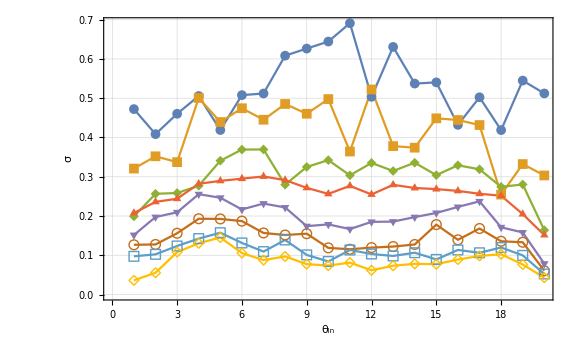

```mathematica
GraphicsRow[{Show[{ListLinePlot[meanscatter,AspectRatio->1,Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}],Show[{ErrorListPlot[meanscatterdatwiderror,AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}]},ImageSize->Large]
ListLinePlot[Sqrt@varscatter[[All,All,2]]*π,Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","σ"}]
```

Comparison of collision curves with different L_p (upper panels). Lower panel: angular fluctuations σ (in rad) for different L_p. θ_in, θ_out and σ in units rad/2.

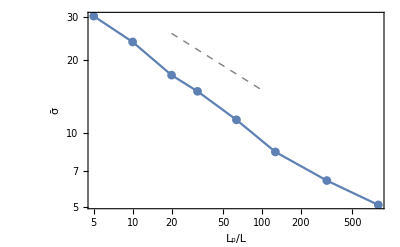

```mathematica
Show[{ListLogLogPlot[Thread@{lps/6.3,180*Sqrt@meanvars},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,Frame->True,FrameLabel->{"L_p/L","σ̄"}],LogLogPlot[70x^{-1/3},{x,20,100},PlotStyle->{Gray,Dashed,Thick}]},PlotRange->All]
```

Averaged angular fluctuations σ̄=<σ>_θ_in as a function of L_p (upper panels). Dashed line corresponds to a power law L_p^(-1/3).